```mathematica
thisIsMyFirstExpression[1 , 2 , 3] = 123;
```

```mathematica
thisIsMyFirstExpression[1 , 2 , 3]
```

123

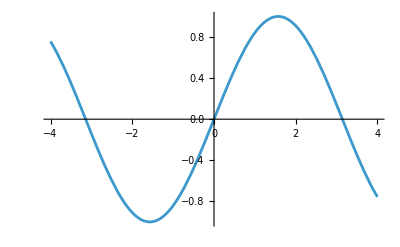

```mathematica
myPlot = Plot[Sin[x] , {x , -4 , 4}]
```

```mathematica
FullForm[myPlot];
```

```mathematica
For[i = 1 , i < 10 , i = i +1 , Print["Hello World!"]]
```

Hello World!

Hello World!

Hello World!

«6 more identical outputs»

```mathematica
Hold[FullForm[Plot[Sin[x] , {x , -4 , 4}]]]
```

Hold[Plot[Sin[x],List[x,-4,4]]]

```mathematica
Hold[FullForm[{1 , 2 , 3}]]
```

Hold[List[1,2,3]]

```mathematica
Plot3D[Sin[x*x + y*y] , {x , -4 , 4} , {y , -4 , 4}]//FullForm
```

```mathematica
?Plot
```

```mathematica
Factorial[0]
```

1

```mathematica
Factorial[1]
```

1

```mathematica
Factorial[2]
```

2

```mathematica
Factorial[123]
```

12146304367025329675766243241881295855454217088483382315328918161829235892362167668831156960612640202170735835221294047782591091570411651472186029519906261646730733907419814952960000000000000000000000000000

```mathematica
silnia[0] = 1;
```

```mathematica
silnia[n_]:=n silnia[n - 1];
```

```mathematica
silnia[123]
```

12146304367025329675766243241881295855454217088483382315328918161829235892362167668831156960612640202170735835221294047782591091570411651472186029519906261646730733907419814952960000000000000000000000000000

```mathematica
Hold[FullForm[silnia[0] = 1]]
```

Hold[Set[silnia[0],1]]

```mathematica
silnia[3]
```

6

```mathematica
Hold[FullForm[silnia[n_]:=n silnia[n - 1]]]
```

Hold[SetDelayed[silnia[Pattern[n,Blank[]]],Times[n,silnia[Plus[n,-1]]]]]

```mathematica
f[x_]:= Sin[x] 10;
```

```mathematica
N[f[1]]
```

8.41471

```mathematica
1.//f
```

8.41471

```mathematica
Hold[FullForm[1.//f]]
```

Hold[f[1.]]

```mathematica
f@1.
```

8.41471

```mathematica
Hold[FullForm[f@1.]]
```

Hold[f[1.]]

```mathematica
g[x_ , y_]:=x + y;
```

```mathematica
g[1. , 2.]
```

3.

```mathematica
1.~g~2.
```

3.

```mathematica
Hold[FullForm[1.~g~2.]]
```

Hold[g[1.,2.]]

```mathematica
gdpPcap = Import["/home/kacpert/Downloads/gdp_pcap.csv"];
```

```mathematica
FullForm[gdpPcap]
```

```mathematica
Head[aaa[bbb[1 , 2 , 3] , fff , ggg , hhh[iii[2]]]]
```

aaa

```mathematica
aaa[bbb[1 , 2 , 3] , fff , ggg , hhh[iii[2]]][[0]]
```

aaa

```mathematica
aaa[bbb[1 , 2 , 3] , fff , ggg , hhh[iii[2]]][[4]]
```

hhh[iii[2]]

```mathematica
aaa[bbb[1 , 2 , 3] , fff , ggg , hhh[iii[2]]][[4]][[1]]
```

iii[2]

```mathematica
aaa[bbb[1 , 2 , 3] , fff , ggg , hhh[iii[2]]][[4]][[1]][[1]]
```

2

```mathematica
aaa[bbb[1 , 2 , 3] , fff , ggg , hhh[iii[2]]][[4,1,1]]
```

2

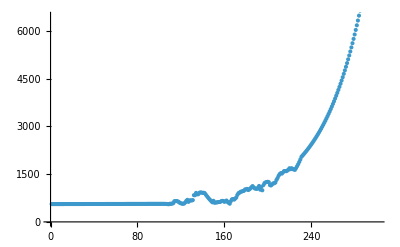

```mathematica
ListPlot[gdpPcap[[123,3;;]]]
```